```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

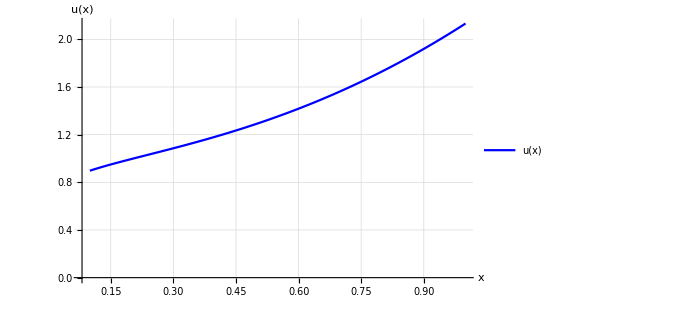

```mathematica
U=Import["solution.txt","Data"];
g1=ListLinePlot[U,GridLines->Full,
PlotStyle->{Blue},
AxesLabel->{Style["x",16,Black,Italic,FontFamily->"Times"],Style["u(x)",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,Arrowheads[{0.0,0.03}],FontFamily->"Times"],
AxesStyle->Thick,
PlotStyle->{Darker[Red,0.4],Thick},
PlotLegends->{"u(x)"},
LabelStyle->Directive[20],
AxesLabel->{"x","u(x)"},
ImageSize->500,
PlotRange->All]
Export["res/g13.pdf",g1];
```

```mathematica
G=Import["solutionSingle.txt","Data"];
g2=ListPointPlot3D[G,
PlotStyle->{Blue},
LabelStyle->Directive[20],
PlotLegends->{"γ(r)"},
AxesLabel->{Style["x",16,Black,Italic,FontFamily->"Times"],Style["y",16,Italic,Black,FontFamily->"Times"],Style["γ(r)",16,Black,Italic,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,Arrowheads[{0.0,0.3}],FontFamily->"Times",AxesStyle->Thick,BoxRatios->{1,1,0.6}],
PlotRange->All,ImageSize->500,
ViewPoint->{Pi,Pi/2,1},
Boxed->False]
```

-Graphics3D-

```mathematica
Export["g2.pdf",g2];
```

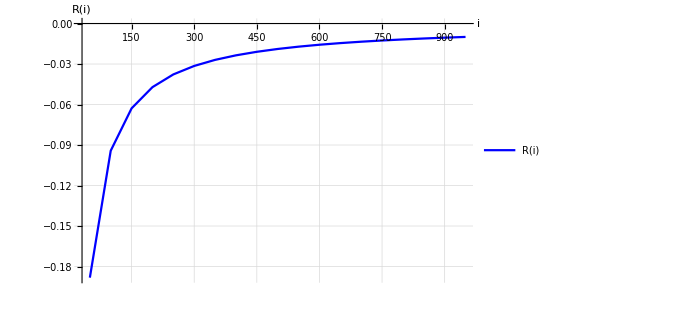

```mathematica
temp=Import["dependency.txt","Data"];
g3=ListLinePlot[temp,GridLines->Full,
PlotStyle->{Blue},
AxesLabel->{Style["i",16,Black,Italic,FontFamily->"Times"],Style["R(i)",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,Arrowheads[{0.0,0.03}],FontFamily->"Times"],
AxesStyle->Thick,
PlotStyle->{Darker[Red,0.4],Thick},
PlotLegends->{"R(i)"},
LabelStyle->Directive[20],
AxesLabel->{"i","R(i)"},
ImageSize->500,
PlotRange->All]
Export["g3.pdf",g3];
```

```mathematica
Log[(5.87*10^-5)/(1.46*10^-5)]
```

1.39142

```mathematica
Log[(1.46*10^-5)/(3.66*10^-6)]
```

1.38356

```mathematica
(1.46*10^-5)/(3.66*10^-6)
```

3.98907

```mathematica
5.86/1.46
```

4.0137

```mathematica
(1.46*10^-5)/(3.65*10^-6)
```

4.

```mathematica
Series[1/2*(1-x*Cos[x*s]),{x,0,8}]
```

1/2-x/2+(s^2 x^3)/4-(s^4 x^5)/48+(s^6 x^7)/1440+O[x]^9

```mathematica
Series[1.0/2*(1.0-x*Cos[x*s]),{x,0,8}]
```

0.5-0.5 x+0.25 s^2 x^3-0.0208333 s^4 x^5+0.000694444 s^6 x^7+O[x]^9

```mathematica
Series[1/2*(1-x*Cos[x*s]),{s,0,8}]
```

(1-x)/2+(x^3 s^2)/4-(x^5 s^4)/48+(x^7 s^6)/1440-(x^9 s^8)/80640+O[s]^9

```mathematica
Series[1.0/2*(1.0-x*Cos[x*s]),{s,0,8}]
```

0.5 (1.-x)+0.25 x^3 s^2-0.0208333 x^5 s^4+0.000694444 x^7 s^6-0.0000124008 x^9 s^8+O[s]^9